```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
rawData=Import["stats.csv"];
```

```mathematica
h=Select[rawData,#⟦1⟧==4∧#⟦2⟧>10&];
```

```mathematica
avgc[x_,n_]:=If[x⟦n*2+2⟧==0,0,x⟦n*2+3⟧/x⟦n*2+2⟧]
```

```mathematica
avgs=Table[avgc[#,n],{n,0,9}]&/@h//N;
```

```mathematica
funcs={Max, Plus, Min}
```

{Max,Plus,Min}

```mathematica
predictData=#[[2;;-1]]->#[[1]]&/@avgs;
```

```mathematica
Predict[predictData]
```

Predict[{{0.00832133,-0.0794823,-0.00645809,-0.0065596,0.0332792,-0.0845653,0.037037,-0.00824374,-0.0539379}→0.047619,«2705»,{0.0083294,-0.0126225,-0.0794615,-0.0034965,0.0108692,0.0333161,0.0034965,-0.0503625,0.00672915}→-0.0967742}]

```mathematica
sects={{2,3,4,5},{6,7,8,9},{10}}
```

{{2,3,4,5},{6,7,8,9},{10}}

```mathematica
pts=Table[{#⟦1⟧,f@@#⟦s⟧}&/@avgs ,{f,funcs},{s,sects}];
```

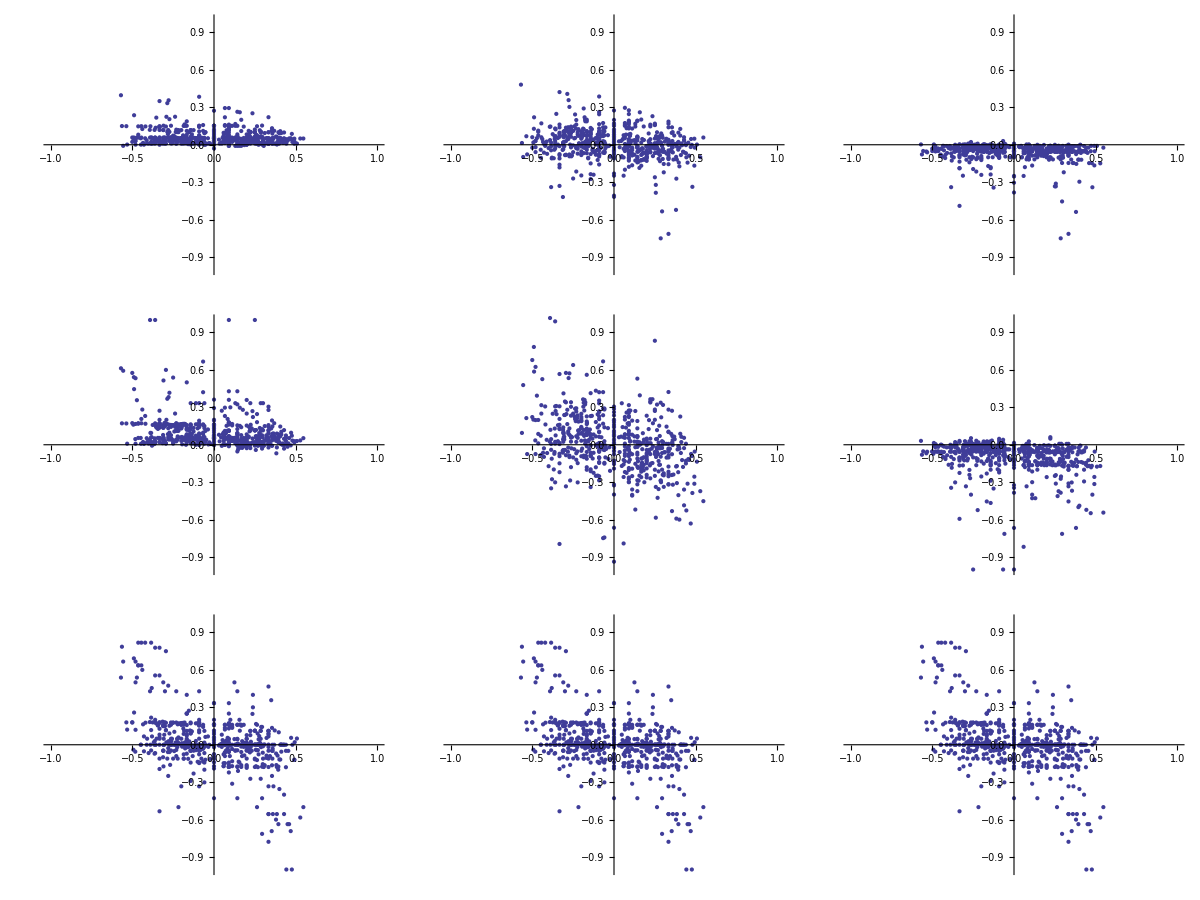

```mathematica
(ListPlot[#,PlotRange->{{-1,1},{-1,1}},ImageSize->Medium]&)/@#&/@pts//Transpose//TableForm
```